1. Parabola

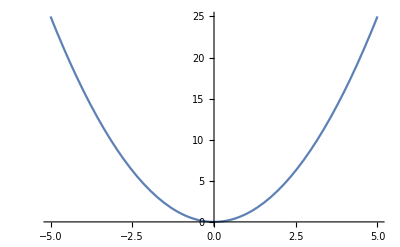

```mathematica
Plot[x^2,{x,-5,5}]
```

2. Kubiskā parabola

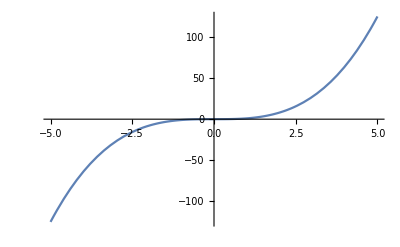

```mathematica
Plot[x^3,{x,-5,5}]
```

3. Vienādsānu hiperbola

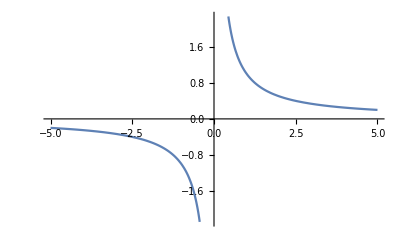

```mathematica
Plot[1/x,{x,-5,5}]
```

4. Parabola (augšējais zars)

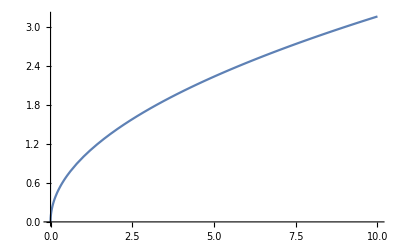

```mathematica
Plot[Sqrt[x],{x,0,10}]
```

5. Kubiskā parabola

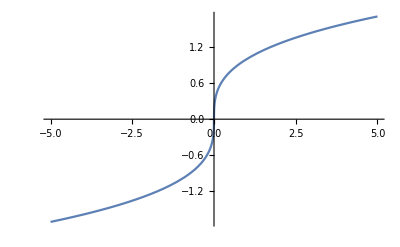

```mathematica
Plot[CubeRoot[x],{x,-5,5}]
```

vai

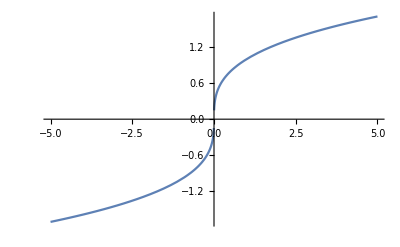

```mathematica
Plot[Sign[x]*Abs[x]^(1/3),{x,-5,5}]
```

6. Puskubiskā parabola

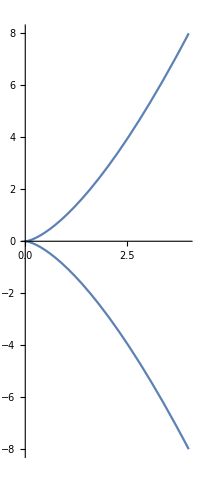

```mathematica
ParametricPlot[{t^2,t^3},{t,-2,2}]
```

7. Neila parabola

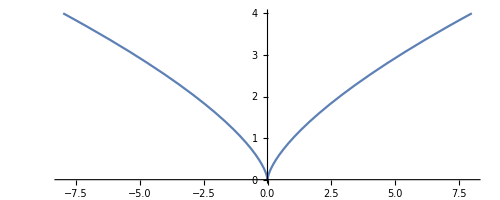

```mathematica
ParametricPlot[{t^3,t^2},{t,-2,2}]
```

8. Daiļveida funkcijas grafiks

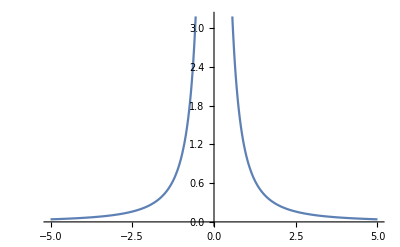

```mathematica
Plot[1/x^2,{x,-5,5}]
```

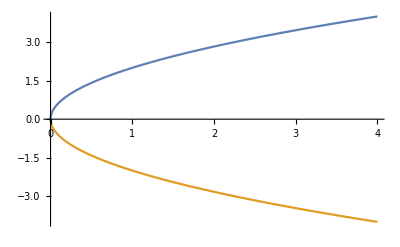

```mathematica
Plot[{2 √x,-2 √x},{x,0,4}]
```

3

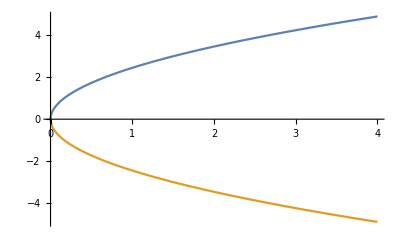

```mathematica
p=3
Plot[{Sqrt[2*p*x],-Sqrt[2*p*x]},{x,0,4}]
```

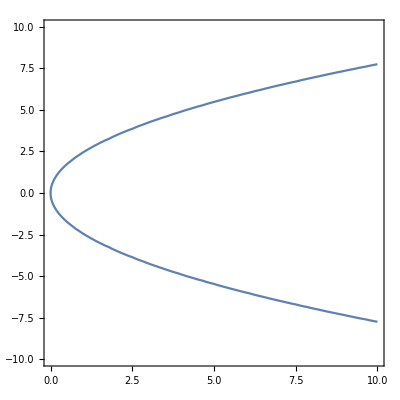

```mathematica
p=3
ContourPlot[y^2==2p*x,{x,0,10},{y,-10,10}]
```

10. Hiperbola

```mathematica
a=2
b=3
```

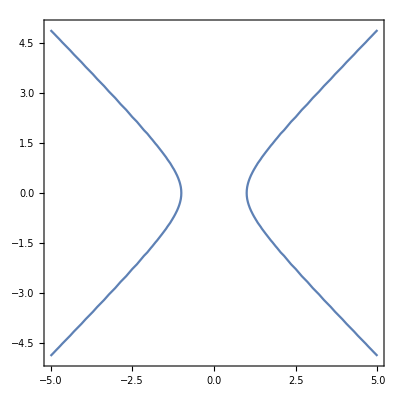

```mathematica
ContourPlot[x*x/a*a-y*y/b*b ==1,{x,-5,5},{y,-5,5},Axes->True]
```

Labajam zaram

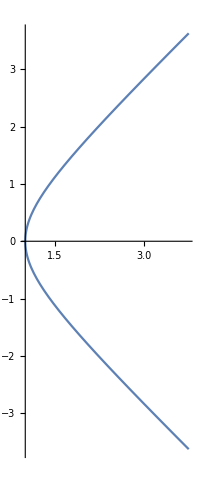

```mathematica
ParametricPlot[{Cosh[t],Sinh[t]},{t,-2,2}]
```

11. Elipse

3

2

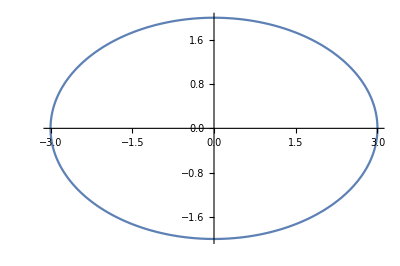

```mathematica
a=3
b=2
ParametricPlot[{a*Cos[t],b*Sin[t]},{t,0,2 Pi}]
```

12. Eksponentfunkciju grafiki

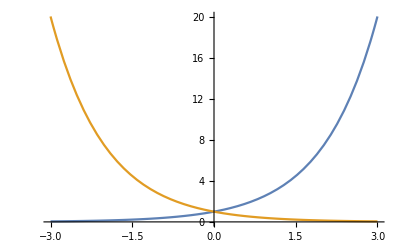

```mathematica
Plot[{ⅇ^x,ⅇ^-x},{x,-3,3}]
```

13. Logaritmiskā līkne

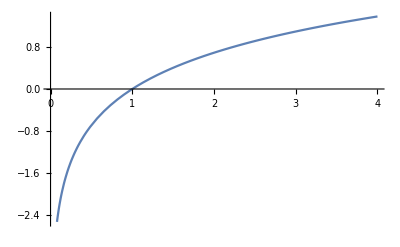

```mathematica
Plot[{Log[ⅇ,x]},{x,0,4}]
```

14. Hiperbolisko funkciju grafiki

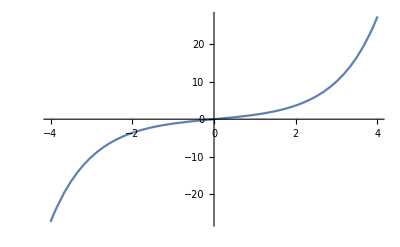

```mathematica
Plot[{Sinh[x]},{x,-4,4}]
```

```mathematica
Plot[{(ⅇ^x-ⅇ^-x)/2},{x,-4,4}]
```

-Graphics-

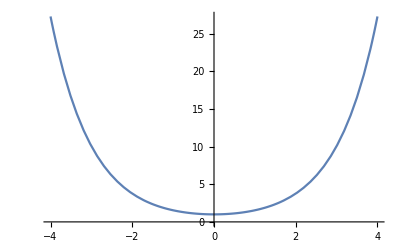

```mathematica
Plot[{Cosh[x]},{x,-4,4}]
```

```mathematica
Plot[{(ⅇ^x+ⅇ^-x)/2},{x,-4,4}]
```

-Graphics-

16. Varbūtību līkne

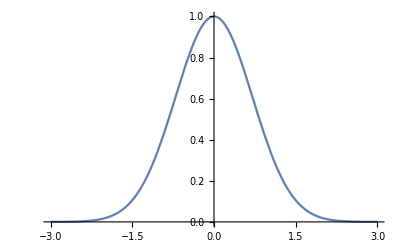

```mathematica
Plot[{ⅇ^(-x^2)},{x,-3,3}]
```

17. Cikloīda

2

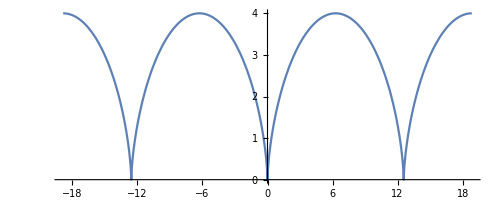

```mathematica
a=2
ParametricPlot[{a*(t-Sin[t]),a*(1-Cos[t])},{t,-3Pi,3 Pi}]
```

18. Astroīda

4

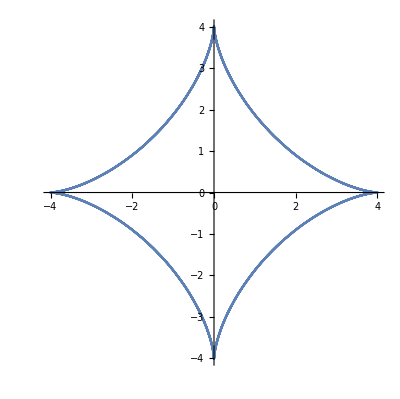

```mathematica
a=4
ParametricPlot[{a*(Cos[t]^3),a*(Sin[t]^3)},{t,-4Pi,4Pi}]
```

19. Traktrise

1

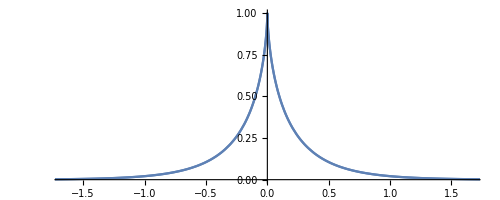

```mathematica
a=1
ParametricPlot[{a*(Cos[t]+Log[ⅇ,Tan[t/2]]),a*(Sin[t]^3)},{t,-2Pi,2Pi}]
```

20. Dekarta lapa

3

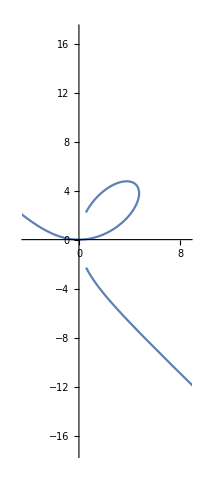

```mathematica
a =3
ParametricPlot[{(3*a*t)/(1+t^3),(3*a*t^2)/(1+t^3)},{t,-4,4}]
```

3

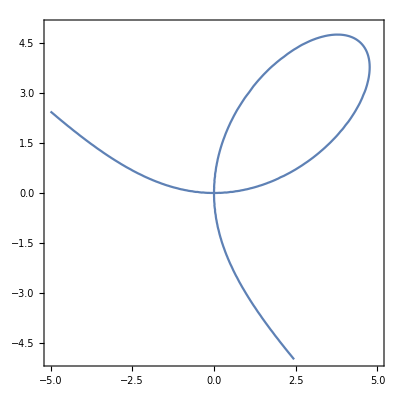

```mathematica
a=3
ContourPlot[x^3+y^3-3*a*x*y==0,{x,-5,5},{y,-5,5},Axes->True]
```

21. Dioklēsa cisoīda

3

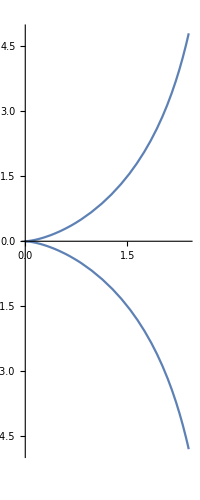

```mathematica
a=3
ParametricPlot[{(a*t^2)/(1+t^2),(a*t^3)/(1+t^2)},{t,-2,2}]
```

22. Strofoīda

1

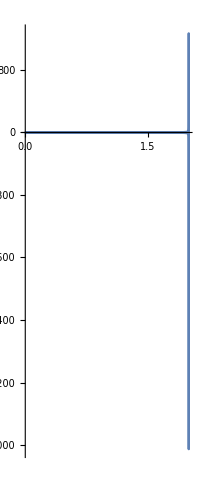

```mathematica
a=1
PolarPlot[(a*(1+Sin[t]))/Cos[t],{t,0,2Pi}]
```

23. Riņķa evolvente

1

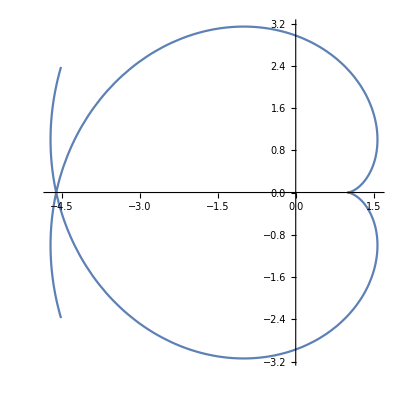

```mathematica
a=1
ParametricPlot[{a*(Cos[t]+t*Sin[t]),a*(Sin[t]-t*Cos[t])},{t,-5,5}]
```

24. Anjēzes līnija

1

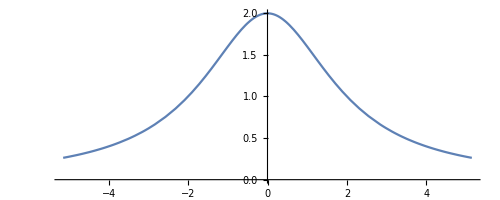

```mathematica
a=1
ParametricPlot[{2*a*Tan[t],2*a*(Cos[t])^2},{t,-1.2,1.2}]
```

25. Arhimeda spirāle

1

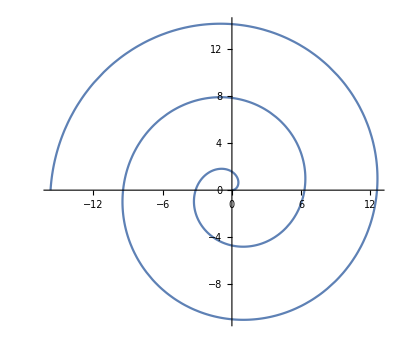

```mathematica
a=1
PolarPlot[a*ϕ,{ϕ,0,5Pi}]
```

26. Hiperboliskā spirāle

1

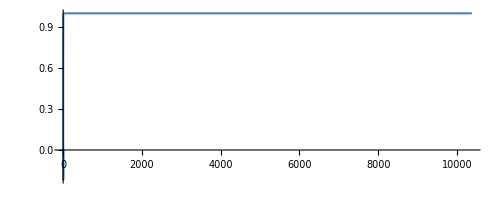

```mathematica
a=1
PolarPlot[a/ϕ,{ϕ,0,2Pi}]
```

27. Logaritmiskā spirāle

1

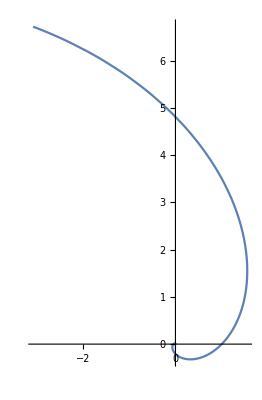

```mathematica
a=1
PolarPlot[ⅇ^(a*ϕ),{ϕ,-6,2}]
```

28. Bernulli lemniskata

1

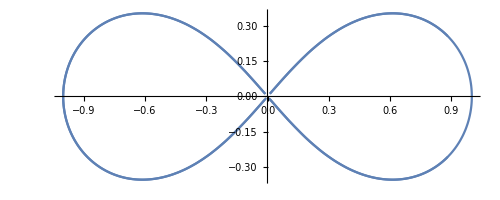

```mathematica
a=1
PolarPlot[√(a^2*Cos[2ϕ]),{ϕ,-6,6}]
```

1

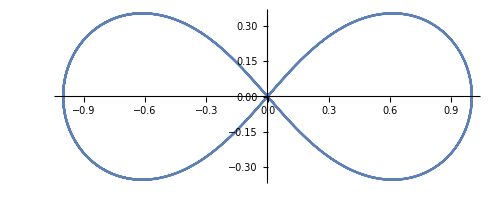

```mathematica
a=1
ParametricPlot[{(a*Cos[t])/(1+(Sin[t])^2),(a*Sin[t]*Cos[t])/(1+(Sin[t])^2)},{t,-10,10}]
```

29. Paskāla līkne

2

1

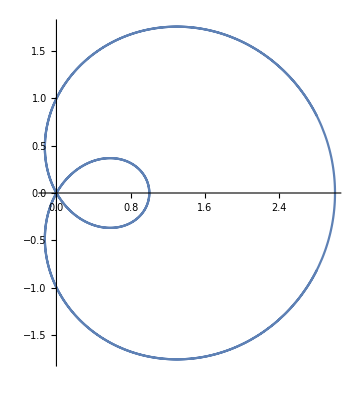

```mathematica
a=2
b=1
PolarPlot[b+a*Cos[ϕ],{ϕ,-6,6}]
```

30. Kordioīda

1

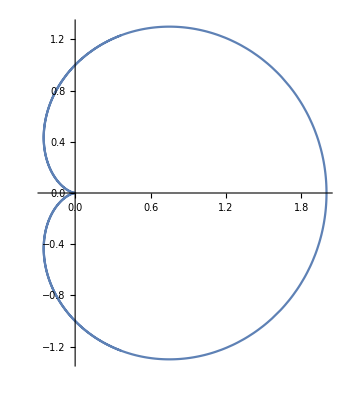

```mathematica
a=1
PolarPlot[a*(1+Cos[ϕ]),{ϕ,-5,5}]
```

31. Kardioīda

1

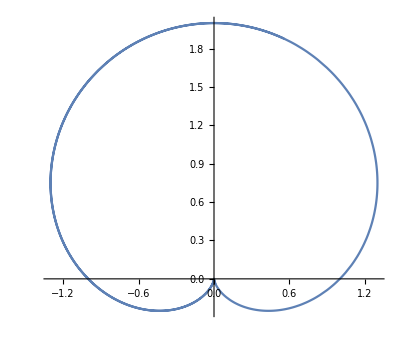

```mathematica
a=1
PolarPlot[a*(1+Sin[ϕ]),{ϕ,-5,5}]
```

32. Kardioīda

1

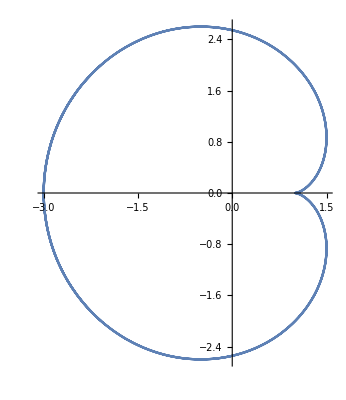

```mathematica
a=1
ParametricPlot[{a*(2*Cos[t]-Cos[2t]),a*(2*Sin[t]-Sin[2t])},{t,-10,10}]
```

33. Trīslapu roze

1

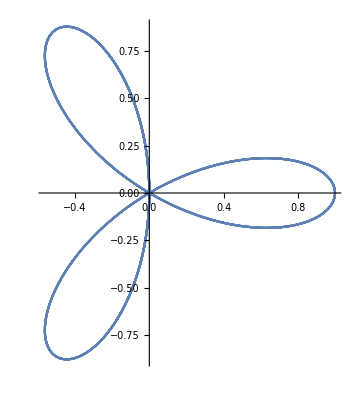

```mathematica
a=1
PolarPlot[a*Cos[3*ϕ],{ϕ,-5,5}]
```

34. Trīslapu roze

1

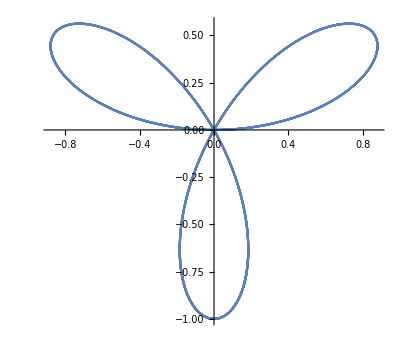

```mathematica
a=1
PolarPlot[a*Sin[3*ϕ],{ϕ,-5,5}]
```

35. Četrlapu roze

1

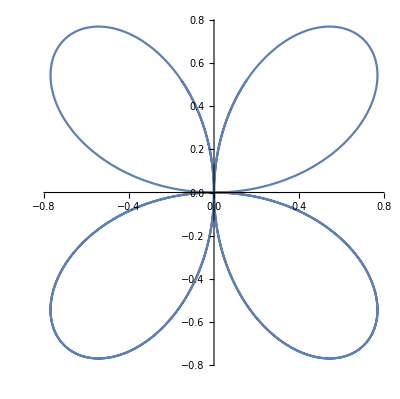

```mathematica
a=1
PolarPlot[a*Sin[2*ϕ],{ϕ,-5,5}]
```

36. Četrlapu roze

1

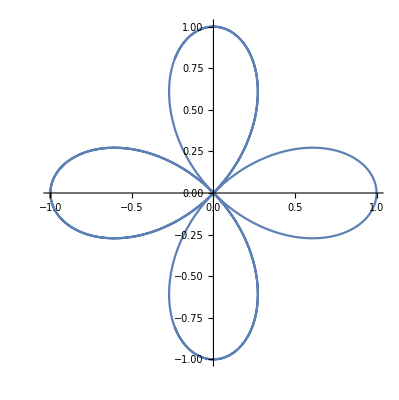

```mathematica
a=1
PolarPlot[a*Cos[2*ϕ],{ϕ,-5,5}]
```

37. Riņķa līnija

1

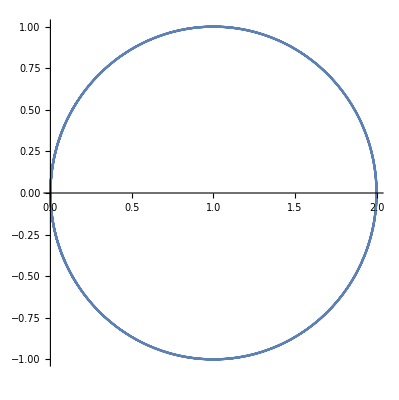

```mathematica
a=1
PolarPlot[2*a*Cos[ϕ],{ϕ,-5,5}]
```

38. Riņķa līnija

1



```mathematica
a=1
PolarPlot[a,{ϕ,0,2Pi}]
```

39. Riņķa līnija

1

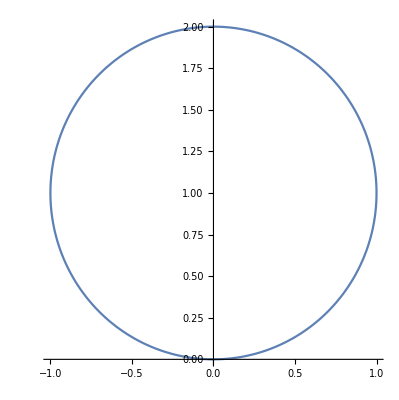

```mathematica
a=1
PolarPlot[2*a*Sin[ϕ],{ϕ,0,Pi}]
```

Stereometrija

1. Riņķa cilindrs

```mathematica
r=1
ContourPlot3D[x^2+y^2==r^2,{x,-2,2},{y,-2,2},{z,-2,2}]
```

1

-Graphics3D-

2. Paraboliskais cilindrs

```mathematica
p=1
ContourPlot3D[x^2==2*p*y,{x,-2,2},{y,-2,2},{z,-2,2}]
```

1

-Graphics3D-

3. Hiperboliskais cilindrs

```mathematica
a=2
b=3
ContourPlot3D[x^2/a^2-y^2/b^2==1,{x,-10,10},{y,-10,10},{z,-10,10}]
```

2

3

-Graphics3D-

4. Konuss

```mathematica
a=1
ContourPlot3D[x^2+y^2==a^2*z^2,{x,-10,10},{y,-10,10},{z,-10,10}]
```

1

-Graphics3D-

5. Sfēra

```mathematica
a=0
b=0
c=0
R=1
ContourPlot3D[(x-a)^2+(y-b)^2+(z-c)^2==R^2,{x,-1,1},{y,-1,1},{z,-1,1}]
```

0

0

0

1

-Graphics3D-

6. Elipsoīds

```mathematica
a=3
b=2
c=2
ContourPlot3D[x^2/a^2+y^2/b^2+z^2/c^2==1,{x,-3,3},{y,-3,3},{z,-3,3}]
```

3

2

2

-Graphics3D-

7. Viendobuma hiperboloīds

```mathematica
a=1
b=1
c=2
ContourPlot3D[x^2/a^2+y^2/b^2-z^2/c^2==1,{x,-3,3},{y,-3,3},{z,-3,3}]
```

1

1

2

-Graphics3D-

8. Divdobumu hiperboloīds

```mathematica
a=1
b=1
c=1
ContourPlot3D[x^2/a^2+y^2/b^2-z^2/c^2==-1,{x,-2,2},{y,-2,2},{z,-2,2}]
```

1

1

1

-Graphics3D-

9. Eliptiskais paraboloīds

```mathematica
a=1
b=1
ContourPlot3D[x^2/a^2+y^2/b^2==z,{x,-1,1},{y,-1,1},{z,-1,1}]
```

1

1

-Graphics3D-

10. Hiperboliskais paraboloīds (seglu virsma)

```mathematica
a=1
b=1
ContourPlot3D[x^2/a^2-y^2/b^2==-z,{x,-1,1},{y,-2,2},{z,-2,2}]
```

1

1

-Graphics3D-

11. Tors

```mathematica
a=3
b=1
ContourPlot3D[(x^2+y^2+z^2+a^2-b^2)^2==4*a^2*(x^2+y^2),{x,-4,4},{y,-4,4},{z,-4,4}]
```

3

1

-Graphics3D-

12. Katenoīds

```mathematica
a=1
b=1
ContourPlot3D[(y^2+z^2)==a^2/4(ⅇ^(x/a)+ⅇ^(-x/a))^2,{x,-2,2},{y,-2,2},{z,-2,2}]
```

1

1

-Graphics3D-

1

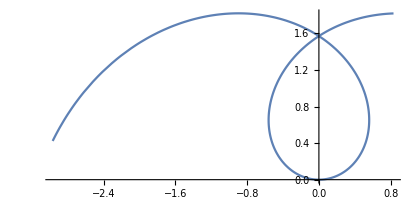

```mathematica
a=1
ParametricPlot[{a*t*Cos[t],a*t*Sin[t]},{t,-2,3}]
```

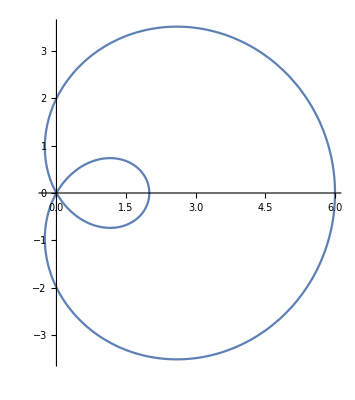

```mathematica
PolarPlot[4Cos[t]-2,{t,0,2Pi}]
```

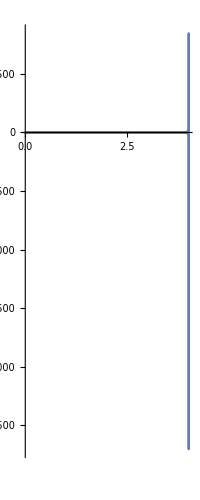

```mathematica
PolarPlot[(2*(1+Sin[t]))/Cos[t],{t,0,2Pi}]
```

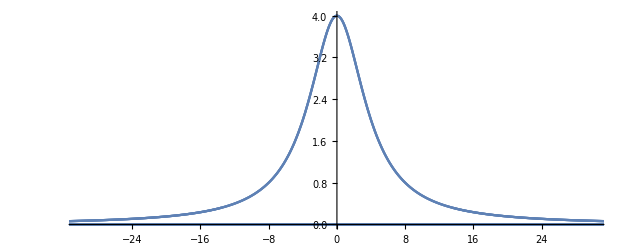

```mathematica
ParametricPlot[{2*2*Tan[t],2*2*(Cos[t])^2},{t,-5,5}]
```

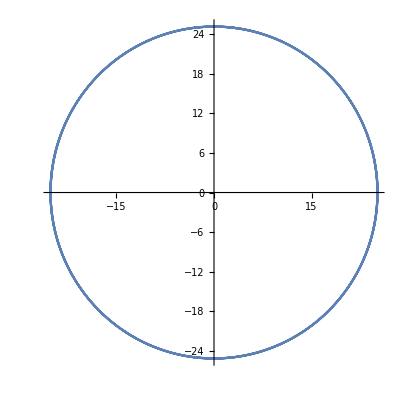

```mathematica
PolarPlot[8*Pi,{t,0,6Pi}]
```

```mathematica
ContourPlot3D[Sqrt[R^2-x^2],{R},{x},{}]
```

```mathematica
ContourPlot[x*x/a*a-y*y/b*b ==1,{x,-5,5},{y,-5,5},Axes->True]
```

```mathematica
ContourPlot3D[x^2+y^2==1,{x,-2,2},{y,-2,2},{R,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u*Cos[a],u*Sin[a],u}{a,0,2Pi},{u,0,2Pi}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2==2*y,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2/3^2-y^2/4^2==1,{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2==2^2*z^2,{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-